```mathematica
(*LIMITS FROM INTEGRAL *)
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.5*10^3*3.086*10^18;(*in cm*)
rs=20*10^3*3.086*10^18;(*in cm*)
rmax=16*10^3*3.086*10^18;(*in cm*)
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
ρ[r_]:=ρ0*(r/r0)^-1*((1+(r0/rs))/(1+(r/rs)))^2
```

```mathematica
emax=3*10^-3;(*in GeV*)
```

```mathematica
emin=0.5*10^-3;(*in GeV*)
```

```mathematica
tage=4.32*10^17;
τ[mpbh_?NumericQ]:=3.28*10^-27*mpbh^3;
```

```mathematica
p[mpbh_?NumericQ]:=Exp[-tage/τ[mpbh]];
```

```mathematica
T[mpbh_?NumericQ,astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ,astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));
```

```mathematica
(*ϕgraham[mpbh_?NumericQ,fpbh_?NumericQ]:=1/(2*π)*NIntegrate[(2*G^2*e^2*mpbh^2*(5.62*10^23)^2)/(Exp[8*π*G*mpbh*5.62*10^23*e]+1),{e,emin,emax}]*NIntegrate[4*π*r^2*ρ[r],{r,0,rmax}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24*p[mpbh]; (*mpbh in g*) (*conversion from GeV to s^-1*)*)


ϕgrahamkerr[mpbh_?NumericQ,fpbh_?NumericQ,astar_?NumericQ]:=1/(2*π)*NIntegrate[(2*2*G^2*(e^2-emin^2)*mpbh^2*(5.62*10^23)^2)/(Exp[(e-omega[mpbh,astar])/T[mpbh,astar]]+1),{e,emin,emax}]*NIntegrate[4*π*r^2*ρ[r],{r,0,rmax}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24*p[mpbh]; (*mpbh in g*) (*conversion from GeV to s^-1*)(* extra factor of 2 due to helicity*)
```

```mathematica
myticks={{{{-9,"10^-9",{0.020,0}},{Log10[2*10^-9],"",{0.010,0}},{Log10[4*10^-9],"",{0.010,0}},{Log10[6*10^-9],"",{0.010,0}},{Log10[8*10^-9],"",{0.010,0}},{-8,"10^-8",{0.020,0}},{Log10[2*10^-8],"",{0.010,0}},{Log10[4*10^-8],"",{0.010,0}},{Log10[6*10^-8],"",{0.010,0}},{Log10[8*10^-8],"",{0.010,0}},{-7,"10^-7",{0.020,0}},{Log10[2*10^-7],"",{0.010,0}},{Log10[4*10^-7],"",{0.010,0}},{Log10[6*10^-7],"",{0.010,0}},{Log10[8*10^-7],"",{0.010,0}},{-6,"10^-6",{0.020,0}},{Log10[2*10^-6],"",{0.010,0}},{Log10[4*10^-6],"",{0.010,0}},{Log10[6*10^-6],"",{0.010,0}},{Log10[8*10^-6],"",{0.010,0}},{-5,"10^-5",{0.020,0}},{Log10[2*10^-5],"",{0.010,0}},{Log10[4*10^-5],"",{0.010,0}},{Log10[6*10^-5],"",{0.010,0}},{Log10[8*10^-5],"",{0.010,0}},{-4,"10^-4",{0.020,0}},{Log10[2*10^-4],"",{0.010,0}},{Log10[4*10^-4],"",{0.010,0}},{Log10[6*10^-4],"",{0.010,0}},{Log10[8*10^-4],"",{0.010,0}},{-3,"10^-3",{0.020,0}},{Log10[2*10^-3],"",{0.010,0}},{Log10[4*10^-3],"",{0.010,0}},{Log10[6*10^-3],"",{0.010,0}},{Log10[8*10^-3],"",{0.010,0}},{-2,"10^-2",{0.020,0}},{Log10[2*10^-2],"",{0.010,0}},{Log10[4*10^-2],"",{0.010,0}},{Log10[6*10^-2],"",{0.010,0}},{Log10[8*10^-2],"",{0.010,0}},{-1,"10^-1",{0.020,0}},{Log10[2*10^-1],"",{0.010,0}},{Log10[4*10^-1],"",{0.010,0}},{Log10[6*10^-1],"",{0.010,0}},{Log10[8*10^-1],"",{0.010,0}}{0,"10^0",{0.020,0}}},None},

{{{14,"10^14",{0.020,0}},{Log10[2*10^14],"",{0.010,0}},{Log10[3*10^14],"",{0.010,0}},{Log10[4*10^14],"",{0.010,0}},{Log10[5*10^14],"",{0.010,0}},{Log10[6*10^14],"",{0.010,0}},{Log10[7*10^14],"",{0.010,0}},{Log10[8*10^14],"",{0.010,0}},{Log10[9*10^14],"",{0.010,0}},{15,"10^15",{0.020,0}},{Log10[2*10^15],"",{0.010,0}},{Log10[3*10^15],"",{0.010,0}},{Log10[4*10^15],"",{0.010,0}},{Log10[5*10^15],"",{0.010,0}},{Log10[6*10^15],"",{0.010,0}},{Log10[7*10^15],"",{0.010,0}},{Log10[8*10^15],"",{0.010,0}},{Log10[9*10^15],"",{0.010,0}},{16,"10^16",{0.020,0}},{Log10[2*10^16],"",{0.010,0}},{Log10[3*10^16],"",{0.010,0}},{Log10[4*10^16],"",{0.010,0}},{Log10[5*10^16],"",{0.010,0}},{Log10[6*10^16],"",{0.010,0}},{Log10[7*10^16],"",{0.010,0}},{Log10[8*10^16],"",{0.010,0}},{Log10[9*10^16],"",{0.010,0}},{17,"10^17",{0.020,0}},{Log10[2*10^17],"",{0.010,0}},{Log10[3*10^17],"",{0.010,0}},{Log10[4*10^17],"",{0.010,0}},{Log10[5*10^17],"",{0.010,0}},{Log10[6*10^17],"",{0.010,0}},{Log10[7*10^17],"",{0.010,0}},{Log10[8*10^17],"",{0.010,0}},{Log10[9*10^17],"",{0.010,0}},{18,"10^18",{0.020,0}},{Log10[2*10^18],"",{0.010,0}},{Log10[3*10^18],"",{0.010,0}},{Log10[4*10^18],"",{0.010,0}},{Log10[5*10^18],"",{0.010,0}},{Log10[6*10^18],"",{0.010,0}},{Log10[7*10^18],"",{0.010,0}},{Log10[8*10^18],"",{0.010,0}},{Log10[9*10^18],"",{0.010,0}},{19,"10^19",{0.020,0}}},None}};
```

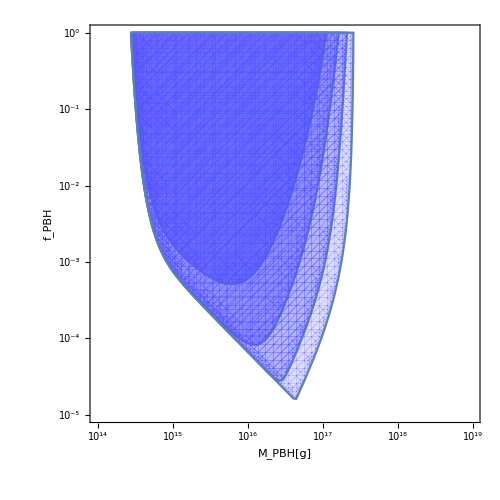

```mathematica
Show[RegionPlot[{ϕgrahamkerr[10^x,10^y,0]>2*10^43},{x,14,19},{y,0,-5},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,PlotStyle->Directive[Lighter[Blue],Opacity[0.6]],FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,GridLines->None,ImageSize->500,PlotPoints->20],RegionPlot[{ϕgrahamkerr[10^x,10^y,0.5]>2*10^43},{x,14,19},{y,0,-5},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,PlotStyle->Directive[Lighter[Blue],Opacity[0.4]],FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},GridLines->None,PlotRangePadding->None,ImageSize->500,PlotPoints->30],RegionPlot[{ϕgrahamkerr[10^x,10^y,0.9]>2*10^43},{x,14,19},{y,0,-5},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,GridLines->None,PlotStyle->Directive[Lighter[Blue],Opacity[0.3]],FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->50],RegionPlot[{ϕgrahamkerr[10^x,10^y,0.9999]>2*10^43},{x,14,19},{y,0,-5},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,GridLines->None,PlotStyle->Directive[Lighter[Blue],Opacity[0.2]],FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,ImageSize->500,PlotPoints->50]]//Quiet
```

```mathematica
(*Survival Probability of primordial blackhole with mass Subscript[M, PBH]*)
```

```mathematica
tage=4.32*10^17;
τ[M_]:=3.28*10^-27*M^3;
```

```mathematica
p[M_]:=Exp[-tage/τ[M]];
```

```mathematica
p[5*10^14]
```

0.34866

```mathematica
(*LIMITS FROM IGRB*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data1=Import["astar0.dat","Table"];
data2=Import["astar0.9.dat","Table"];
data3=Import["astar0.9999.dat","Table"];
myticks={{{{-9,"10^-9",{0.020,0}},{Log10[2*10^-9],"",{0.010,0}},{Log10[4*10^-9],"",{0.010,0}},{Log10[6*10^-9],"",{0.010,0}},{Log10[8*10^-9],"",{0.010,0}},{-8,"10^-8",{0.020,0}},{Log10[2*10^-8],"",{0.010,0}},{Log10[4*10^-8],"",{0.010,0}},{Log10[6*10^-8],"",{0.010,0}},{Log10[8*10^-8],"",{0.010,0}},{-7,"10^-7",{0.020,0}},{Log10[2*10^-7],"",{0.010,0}},{Log10[4*10^-7],"",{0.010,0}},{Log10[6*10^-7],"",{0.010,0}},{Log10[8*10^-7],"",{0.010,0}},{-6,"10^-6",{0.020,0}},{Log10[2*10^-6],"",{0.010,0}},{Log10[4*10^-6],"",{0.010,0}},{Log10[6*10^-6],"",{0.010,0}},{Log10[8*10^-6],"",{0.010,0}},{-5,"10^-5",{0.020,0}},{Log10[2*10^-5],"",{0.010,0}},{Log10[4*10^-5],"",{0.010,0}},{Log10[6*10^-5],"",{0.010,0}},{Log10[8*10^-5],"",{0.010,0}},{-4,"10^-4",{0.020,0}},{Log10[2*10^-4],"",{0.010,0}},{Log10[4*10^-4],"",{0.010,0}},{Log10[6*10^-4],"",{0.010,0}},{Log10[8*10^-4],"",{0.010,0}},{-3,"10^-3",{0.020,0}},{Log10[2*10^-3],"",{0.010,0}},{Log10[4*10^-3],"",{0.010,0}},{Log10[6*10^-3],"",{0.010,0}},{Log10[8*10^-3],"",{0.010,0}},{-2,"10^-2",{0.020,0}},{Log10[2*10^-2],"",{0.010,0}},{Log10[4*10^-2],"",{0.010,0}},{Log10[6*10^-2],"",{0.010,0}},{Log10[8*10^-2],"",{0.010,0}},{-1,"10^-1",{0.020,0}},{Log10[2*10^-1],"",{0.010,0}},{Log10[4*10^-1],"",{0.010,0}},{Log10[6*10^-1],"",{0.010,0}},{Log10[8*10^-1],"",{0.010,0}}{0,"10^0",{0.020,0}}},None},

{{{14,"10^14",{0.020,0}},{Log10[2*10^14],"",{0.010,0}},{Log10[3*10^14],"",{0.010,0}},{Log10[4*10^14],"",{0.010,0}},{Log10[5*10^14],"",{0.010,0}},{Log10[6*10^14],"",{0.010,0}},{Log10[7*10^14],"",{0.010,0}},{Log10[8*10^14],"",{0.010,0}},{Log10[9*10^14],"",{0.010,0}},{15,"10^15",{0.020,0}},{Log10[2*10^15],"",{0.010,0}},{Log10[3*10^15],"",{0.010,0}},{Log10[4*10^15],"",{0.010,0}},{Log10[5*10^15],"",{0.010,0}},{Log10[6*10^15],"",{0.010,0}},{Log10[7*10^15],"",{0.010,0}},{Log10[8*10^15],"",{0.010,0}},{Log10[9*10^15],"",{0.010,0}},{16,"10^16",{0.020,0}},{Log10[2*10^16],"",{0.010,0}},{Log10[3*10^16],"",{0.010,0}},{Log10[4*10^16],"",{0.010,0}},{Log10[5*10^16],"",{0.010,0}},{Log10[6*10^16],"",{0.010,0}},{Log10[7*10^16],"",{0.010,0}},{Log10[8*10^16],"",{0.010,0}},{Log10[9*10^16],"",{0.010,0}},{17,"10^17",{0.020,0}},{Log10[2*10^17],"",{0.010,0}},{Log10[3*10^17],"",{0.010,0}},{Log10[4*10^17],"",{0.010,0}},{Log10[5*10^17],"",{0.010,0}},{Log10[6*10^17],"",{0.010,0}},{Log10[7*10^17],"",{0.010,0}},{Log10[8*10^17],"",{0.010,0}},{Log10[9*10^17],"",{0.010,0}},{18,"10^18",{0.020,0}}},None}};
```

```mathematica
p=ListPlot[Table[{Log10[10^14*data1[[i,1]]],Log10[data1[[i,2]]]},{i,Length[data1]}],PlotRange->{{15,18},{0,-9}},PlotStyle->Darker[Cyan],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->500,AspectRatio->1,Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];
```

```mathematica
q=ListPlot[Table[{Log10[10^14*data2[[i,1]]],Log10[data2[[i,2]]]},{i,Length[data2]}],PlotRange->{{14,18},{0,-9}},PlotStyle->Darker[Cyan],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->500,AspectRatio->1,Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];
```

```mathematica
r=ListPlot[Table[{Log10[10^14*data3[[i,1]]],Log10[data3[[i,2]]]},{i,Length[data3]}],PlotRange->{{14,18},{0,-9}},PlotStyle->Darker[Cyan],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->500,AspectRatio->1,Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];
```

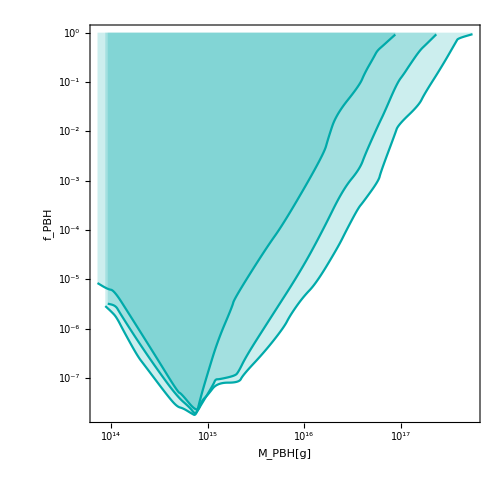

```mathematica
Show[p,q,r]
```

```mathematica
(*COMBINED LIMIT*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
wddata=Import["wd.dat","Table"];
keplerdata=Import["kepler.dat","Table"];
subarudata=Import["subaru_v2.dat","Table"];
machodata=Import["macho.dat","Table"];
```

```mathematica
firasdata=Import["firas_new.dat","Table"];
lssdata=Import["lss.dat","Table"];
dwarfdata=Import["ufd_v2.dat","Table"];
wbdata=Import["wb.dat","Table"];
mlqdata=Import["mlq.dat","Table"];
dfdata=Import["df.dat","Table"];
```

```mathematica
wmapdata=Import["wmap_v2.dat","Table"];
voyagerdata=Import["voyagerred_v3.dat","Table"];
```

```mathematica
egdata=Import["egb_v3.dat","Table"];
```

```mathematica
edgesdata=Import["21cm.dat","Table"];
femtodata=Import["femtolensing.dat","Table"];
nsdata=Import["ns.dat","Table"];
o2data=Import["o2.dat","Table"];
sndata=Import["snlensing.dat","Table"];
o1data=Import["o1.dat","Table"];
o1datamodi=10^o1data;
myticks={{{{-5,"10^-5",{0.010,0}},{Log10[2*10^-5],"",{0.005,0}},{Log10[3*10^-5],"",{0.005,0}},{Log10[4*10^-5],"",{0.005,0}},{Log10[5*10^-5],"",{0.005,0}},{Log10[6*10^-5],"",{0.005,0}},{Log10[7*10^-5],"",{0.005,0}},{Log10[8*10^-5],"",{0.005,0}},{Log10[9*10^-5],"",{0.005,0}},{-4,"10^-4",{0.010,0}},{Log10[2*10^-4],"",{0.005,0}},{Log10[3*10^-4],"",{0.005,0}},{Log10[4*10^-4],"",{0.005,0}},{Log10[5*10^-4],"",{0.005,0}},{Log10[6*10^-4],"",{0.005,0}},{Log10[7*10^-4],"",{0.005,0}},{Log10[8*10^-4],"",{0.005,0}},{Log10[9*10^-4],"",{0.005,0}},{-3,"10^-3",{0.010,0}},{Log10[2*10^-3],"",{0.005,0}},{Log10[3*10^-3],"",{0.005,0}},{Log10[4*10^-3],"",{0.005,0}},{Log10[5*10^-3],"",{0.005,0}},{Log10[6*10^-3],"",{0.005,0}},{Log10[7*10^-3],"",{0.005,0}},{Log10[8*10^-3],"",{0.005,0}},{Log10[9*10^-3],"",{0.005,0}},{-2,"10^-2",{0.010,0}},{Log10[2*10^-2],"",{0.005,0}},{Log10[3*10^-2],"",{0.005,0}},{Log10[4*10^-2],"",{0.005,0}},{Log10[5*10^-2],"",{0.005,0}},{Log10[6*10^-2],"",{0.005,0}},{Log10[7*10^-2],"",{0.005,0}},{Log10[8*10^-2],"",{0.005,0}},{Log10[9*10^-2],"",{0.005,0}},{-1,"10^-1",{0.010,0}},{Log10[2*10^-1],"",{0.005,0}},{Log10[3*10^-1],"",{0.005,0}},{Log10[4*10^-1],"",{0.005,0}},{Log10[5*10^-1],"",{0.005,0}},{Log10[6*10^-1],"",{0.005,0}},{Log10[7*10^-1],"",{0.005,0}},{Log10[8*10^-1],"",{0.005,0}},{Log10[9*10^-1],"",{0.005,0}},{0,"10^0",{0.010,0}}},{{-4,"",{0.010,0}},{Log10[2*10^-4],"",{0.005,0}},{Log10[3*10^-4],"",{0.005,0}},{Log10[4*10^-4],"",{0.005,0}},{Log10[5*10^-4],"",{0.005,0}},{Log10[6*10^-4],"",{0.005,0}},{Log10[7*10^-4],"",{0.005,0}},{Log10[8*10^-4],"",{0.005,0}},{Log10[9*10^-4],"",{0.005,0}},{-3,"",{0.010,0}},{Log10[2*10^-3],"",{0.005,0}},{Log10[3*10^-3],"",{0.005,0}},{Log10[4*10^-3],"",{0.005,0}},{Log10[5*10^-3],"",{0.005,0}},{Log10[6*10^-3],"",{0.005,0}},{Log10[7*10^-3],"",{0.005,0}},{Log10[8*10^-3],"",{0.005,0}},{Log10[9*10^-3],"",{0.005,0}},{-2,"",{0.010,0}},{Log10[2*10^-2],"",{0.005,0}},{Log10[3*10^-2],"",{0.005,0}},{Log10[4*10^-2],"",{0.005,0}},{Log10[5*10^-2],"",{0.005,0}},{Log10[6*10^-2],"",{0.005,0}},{Log10[7*10^-2],"",{0.005,0}},{Log10[8*10^-2],"",{0.005,0}},{Log10[9*10^-2],"",{0.005,0}},{-1,"",{0.010,0}},{Log10[2*10^-1],"",{0.005,0}},{Log10[3*10^-1],"",{0.005,0}},{Log10[4*10^-1],"",{0.005,0}},{Log10[5*10^-1],"",{0.005,0}},{Log10[6*10^-1],"",{0.005,0}},{Log10[7*10^-1],"",{0.005,0}},{Log10[8*10^-1],"",{0.005,0}},{Log10[9*10^-1],"",{0.005,0}},{0,"",{0.010,0}}}},

{{{14,"10^14",{0.010,0}},{15,"10^15",{0.010,0}},{16,"10^16",{0.010,0}},{17,"10^17",{0.010,0}},{18,"10^18",{0.010,0}},{19,"10^19",{0.010,0}},{20,"10^20",{0.010,0}},{21,"10^21",{0.010,0}},{22,"10^22",{0.010,0}},{23,"10^23",{0.010,0}},{24,"10^24",{0.010,0}},{25,"10^25",{0.010,0}},{26,"10^26",{0.010,0}},{27,"10^27",{0.010,0}},{28,"10^28",{0.010,0}},{29,"10^29",{0.010,0}},{30,"10^30",{0.010,0}},{31,"10^31",{0.010,0}},{32,"10^32",{0.010,0}},{33,"10^33",{0.010,0}},{34,"10^34",{0.010,0}},{35,"10^35",{0.010,0}},{36,"10^36",{0.010,0}},{37,"10^37",{0.010,0}},{38,"10^38",{0.010,0}},{39,"10^39",{0.010,0}},{40,"10^40",{0.010,0}},{41,"10^41",{0.010,0}},{42,"10^42",{0.010,0}},{43,"10^43",{0.010,0}}},{{Log10[2*10^14],"10^-19",{0.010,0}},{Log10[2*10^15],"",{0.010,0}},{Log10[2*10^16],"10^-17",{0.010,0}},{Log10[2*10^17],"",{0.010,0}},{Log10[2*10^18],"10^-15",{0.010,0}},{Log10[2*10^19],"",{0.010,0}},{Log10[2*10^20],"10^-13",{0.010,0}},{Log10[2*10^21],"",{0.010,0}},{Log10[2*10^22],"10^-11",{0.010,0}},{Log10[2*10^23],"",{0.010,0}},{Log10[2*10^24],"10^-9",{0.010,0}},{Log10[2*10^25],"",{0.010,0}},{Log10[2*10^26],"10^-7",{0.010,0}},{Log10[2*10^27],"",{0.010,0}},{Log10[2*10^28],"10^-5",{0.010,0}},{Log10[2*10^29],"",{0.010,0}},{Log10[2*10^30],"10^-3",{0.010,0}},{Log10[2*10^31],"",{0.010,0}},{Log10[2*10^32],"10^-1",{0.010,0}},{Log10[2*10^33],"",{0.010,0}},{Log10[2*10^34],"10^1",{0.010,0}},{Log10[2*10^35],"",{0.010,0}},{Log10[2*10^36],"10^3",{0.010,0}},{Log10[2*10^37],"",{0.010,0}},{Log10[2*10^38],"10^5",{0.010,0}},{Log10[2*10^39],"",{0.010,0}},{Log10[2*10^40],"10^7",{0.010,0}},{Log10[2*10^41],"",{0.010,0}},{Log10[2*10^42],"10^9",{0.010,0}}}}};
```

```mathematica
a1=ListPlot[Table[{Log10[10^16*wddata[[i,1]]],Log10[wddata[[i,2]]]},{i,Length[wddata]}],PlotRange->{{15,37},{0,-6}},PlotStyle->{Darker[Red],Dashed},Frame->True,FrameStyle->Directive[20, "Times",Black,Thickness[0.001]],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 2,FrameLabel->{{Style["f_PBH",FontSize->40,Bold],None},{Style["M_PBH[g]",FontSize->40,Bold],Style["M_PBH/\!\(\*SubscriptBox[\(M\), \(⊙\)]\)",FontSize->40]}},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

a2=ListPlot[Table[{Log10[10^16*keplerdata[[i,1]]],Log10[keplerdata[[i,2]]]},{i,Length[keplerdata]}],PlotRange->{{15,37},{0,-5}},PlotStyle->{Darker[Gray]},Frame->True,FrameStyle->Directive[20, "Times",Black,Thickness[0.001]],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 2,FrameLabel->{{Style["f_PBH",FontSize->40],None},{Style["M_PBH [g]",FontSize->40],Style[Style["M_PBH/\!\(\*SubscriptBox[\(M\), \(⊙\)]\)",FontSize->40],FontSize->20]}},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

a3=ListPlot[Table[{Log10[10^20*subarudata[[i,1]]],Log10[subarudata[[i,2]]]},{i,Length[subarudata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

a4=ListPlot[Table[{Log10[10^16*machodata[[i,1]]],Log10[machodata[[i,2]]]},{i,Length[machodata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

a5=ListPlot[Table[{Log10[2*10^33*firasdata[[i,1]]],Log10[firasdata[[i,2]]]},{i,Length[firasdata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Red],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];


a6=ListPlot[Table[{Log10[2*10^33*wmapdata[[i,1]]],Log10[wmapdata[[i,2]]]},{i,Length[wmapdata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

a7=ListPlot[Table[{Log10[10^16*femtodata[[i,1]]],Log10[femtodata[[i,2]]]},{i,Length[femtodata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->{Darker[Red],Dotted},Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

a8=ListPlot[Table[{Log10[10^19*nsdata[[i,1]]],Log10[nsdata[[i,2]]]},{i,Length[nsdata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->{Darker[Red],Dashed},Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

a9=ListPlot[Table[{Log10[10^16*lssdata[[i,1]]],Log10[lssdata[[i,2]]]},{i,Length[lssdata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 1,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

a10=ListPlot[Table[{Log10[10^16*dwarfdata[[i,1]]],Log10[dwarfdata[[i,2]]]},{i,Length[dwarfdata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 1,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

a11=ListPlot[Table[{Log10[10^16*wbdata[[i,1]]],Log10[wbdata[[i,2]]]},{i,Length[wbdata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Red],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];


a12=ListPlot[Table[{Log10[10^16*mlqdata[[i,1]]],Log10[mlqdata[[i,2]]]},{i,Length[mlqdata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Red],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 1,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

a13=ListPlot[Table[{Log10[10^16*dfdata[[i,1]]],Log10[dfdata[[i,2]]]},{i,Length[dfdata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Red],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->1300,AspectRatio->0.5,Joined->True,InterpolationOrder-> 1,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},FrameTicks->myticks,PlotRangePadding->None,Filling->Top];

a14=ListPlot[Table[{Log10[10^15*voyagerdata[[i,1]]],Log10[10^-9*voyagerdata[[i,2]]]},{i,Length[voyagerdata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Green],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top];

a15=ListPlot[Table[{Log10[10^15*egdata[[i,1]]],Log10[10^-9*egdata[[i,2]]]},{i,Length[egdata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Orange],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top];

a16=ListPlot[Table[{Log10[2*10^33*o2data[[i,1]]],Log10[o2data[[i,2]]]},{i,Length[o2data]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 1,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top];

a17=ListPlot[Table[{Log10[2*10^33*sndata[[i,1]]],Log10[sndata[[i,2]]]},{i,Length[sndata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 1,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top];

a18=ListPlot[Table[{Log10[2*10^33*o1datamodi[[i,1]]],Log10[o1datamodi[[i,2]]]},{i,Length[o1datamodi]}],PlotRange->{{14,37},{0,-7}},PlotStyle->Darker[Gray],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top];


a19=ListPlot[Table[{Log10[edgesdata[[i,1]]],edgesdata[[i,2]]},{i,Length[edgesdata]}],PlotRange->{{14,37},{0,-7}},PlotStyle->RGBColor["#934B00"],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,InterpolationOrder-> 2,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::ioproc: {{19.0931, -0.02}, {19.0931, -0.264444}, {19.0863, -0.557778}, <<548>>, {0.434294 Log[1. Power[10, 16] fluxe<<8>>(df)], <<1>>}, {0.434294 Log[1. Power[10, 16] return], 0.434294 Log[fluxes]}} may contain non-machine-precision numbers, complex numbers, or invalid entries.

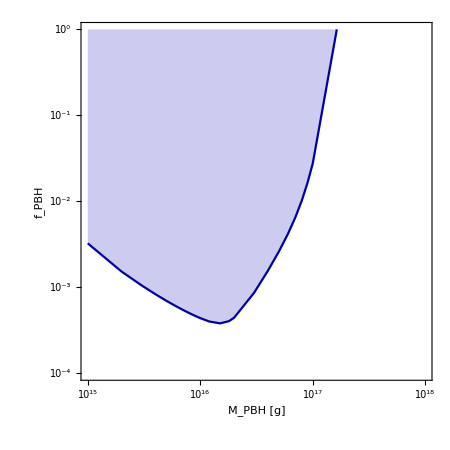
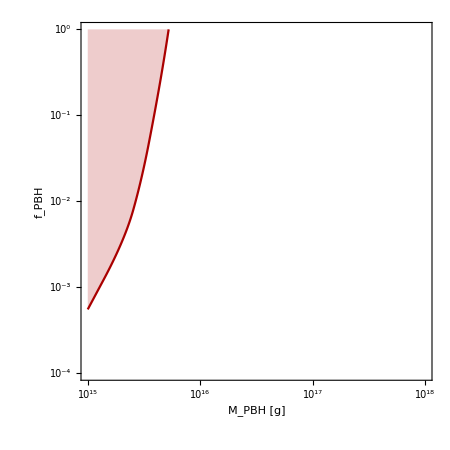
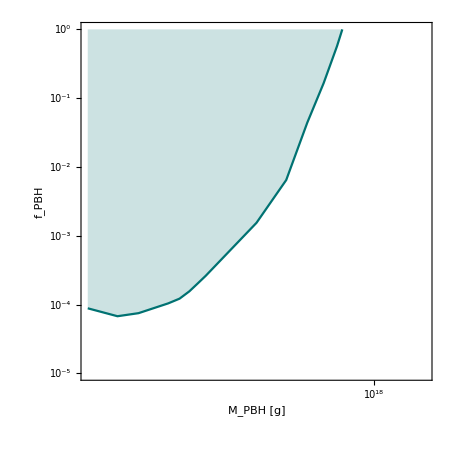
```mathematica
p=Show[a2,a3,a4,a6,a9,a10,a13,a16,a17,a18,a19,-Graphics-,-Graphics-,-Graphics-]
```

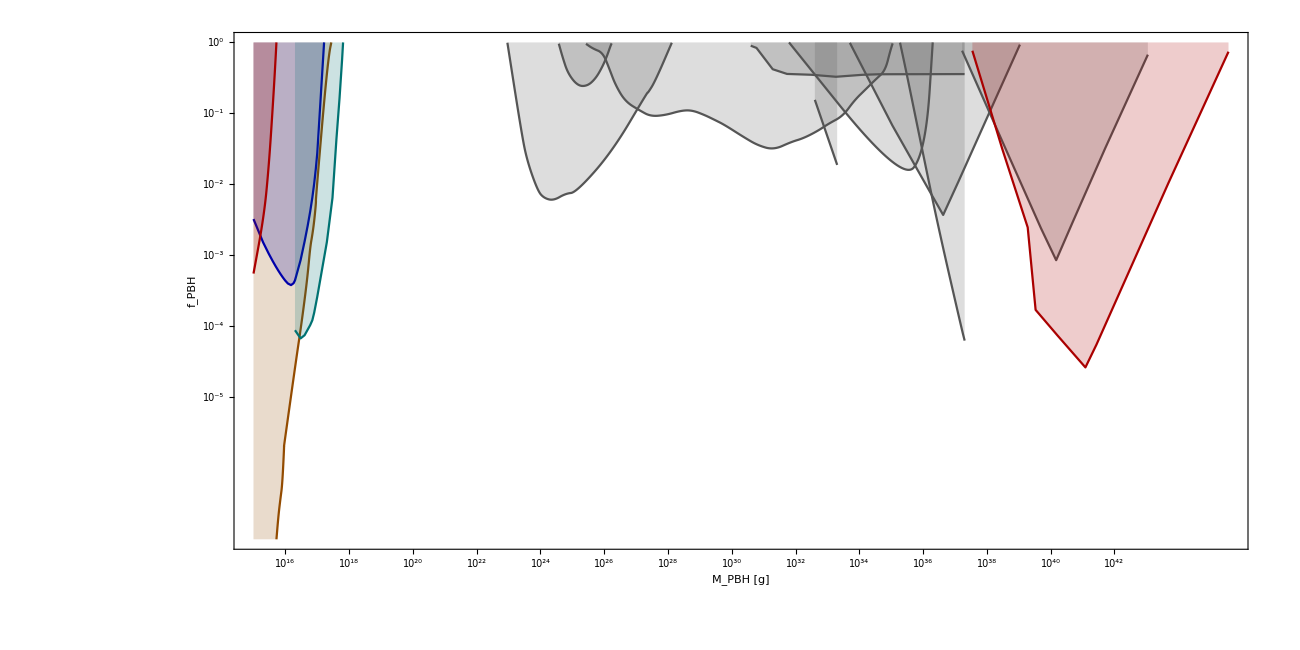

```mathematica
edgesdata//Length
```

41

```mathematica
(*Export["combined.pdf",p];*)
```

```mathematica
Export["combined_astar0.pdf",p];
```

```mathematica
(*Limits from Voyager*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
voyagerdata=Import["voyager_data.dat","Table"];
```

```mathematica
p=ListLogLogPlot[Table[{voyagerdata[[i,1]],voyagerdata[[i,2]]},{i,Length[voyagerdata]}],PlotRange->{{10^-3,10},{10^7,10^-9}},PlotStyle->Darker[Red],Frame->True,FrameStyle->Directive[14, "Times",Black],ImageSize->500,AspectRatio->0.5,Joined->False];
```

```mathematica
Get["btot.m"];
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.5*10^3*3.086*10^18;(*in cm*)
rs=20*10^3*3.086*10^18;(*in cm*)
rmax=15*10^3*3.086*10^18;(*in cm*)(*15 kpc is roughly the size of our galaxy*)
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
ρ[r_]:=ρ0*(r/r0)^-1*((1+(r0/rs))/(1+(r/rs)))^2;
```

```mathematica
T[mpbh_?NumericQ,astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*) 
omega[mpbh_?NumericQ,astar_?NumericQ]:=astar/(2*G*mpbh*5.62*10^23*(1+(1-astar^2)^0.5));
```

```mathematica
Q[e1_,r_,astar_,mpbh_]:=1/(2*π)*(27*G^2*e1^2*mpbh^2*(5.62*10^23)^2)/(Exp[(e1-omega[mpbh,astar])/T[mpbh,astar]]+1)*1.52*10^24*ρ[r]/(mpbh*5.62*10^23);
```

```mathematica
ϕ[e_,mpbh_]:=(3*10^10)/(4*π*btot[e,8.5,0,1,"MF1"])*NIntegrate[Q[e1,r0,0,mpbh],{e1,e,∞}];
```

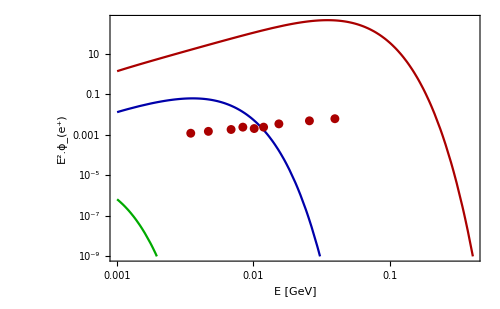

```mathematica
Show[LogLogPlot[e^2*ϕ[e,10^15],{e,10^-3,10},PlotRange->{10^7,10^-9},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["E [GeV]",FontSize->20,Bold],Style["E^2.ϕ_(e^+)",FontSize->20,Bold]},PlotRangePadding->None,PlotStyle->Darker[Red],ImageSize->500],LogLogPlot[e^2*ϕ[e,10^16],{e,10^-3,10},PlotRange->{10^7,10^-9},Frame->True,FrameStyle->Directive[14, "Times",Black],AspectRatio->1,FrameLabel->{Style["E [GeV]",FontSize->20,Bold],Style["E^2.ϕ_(e^+)",FontSize->20,Bold]},PlotRangePadding->None,PlotStyle->Darker[Blue],ImageSize->700],LogLogPlot[e^2*ϕ[e,10^17],{e,10^-3,10},PlotRange->{10^7,10^-9},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameLabel->{Style["E [GeV]",FontSize->20,Bold],Style["E^2.ϕ_(e^+)",FontSize->20,Bold]},PlotRangePadding->None,PlotStyle->Darker[Green],ImageSize->500],p]
```

```mathematica
(*COMBINING KAMLAND AND SUPER-K *)(*ONLY GALACTIC*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
astarkamland1=Import["kamland_astar_0.9.dat","Table"];
```

```mathematica
astarkamland2=Import["kamland_astar_0.9999.dat","Table"];
astarkamland3=Import["kamland_astar_0.5.dat","Table"];
astarkamland4=Import["kamland_astar_0.dat","Table"];
```

```mathematica
astarsuperk1=Import["superk_astar_0.9.dat","Table"];
```

```mathematica
astarsuperk2=Import["superk_astar_0.9999.dat","Table"];
astarsuperk3=Import["superk_astar_0.5.dat","Table"];
astarsuperk4=Import["superk_astar_0.dat","Table"];
```

```mathematica
myticks={{{{-9,"10^-9",{0.020,0}},{Log10[2*10^-9],"",{0.010,0}},{Log10[4*10^-9],"",{0.010,0}},{Log10[6*10^-9],"",{0.010,0}},{Log10[8*10^-9],"",{0.010,0}},{-8,"10^-8",{0.020,0}},{Log10[2*10^-8],"",{0.010,0}},{Log10[4*10^-8],"",{0.010,0}},{Log10[6*10^-8],"",{0.010,0}},{Log10[8*10^-8],"",{0.010,0}},{-7,"10^-7",{0.020,0}},{Log10[2*10^-7],"",{0.010,0}},{Log10[4*10^-7],"",{0.010,0}},{Log10[6*10^-7],"",{0.010,0}},{Log10[8*10^-7],"",{0.010,0}},{-6,"10^-6",{0.020,0}},{Log10[2*10^-6],"",{0.010,0}},{Log10[4*10^-6],"",{0.010,0}},{Log10[6*10^-6],"",{0.010,0}},{Log10[8*10^-6],"",{0.010,0}},{-5,"10^-5",{0.020,0}},{Log10[2*10^-5],"",{0.010,0}},{Log10[4*10^-5],"",{0.010,0}},{Log10[6*10^-5],"",{0.010,0}},{Log10[8*10^-5],"",{0.010,0}},{-4,"10^-4",{0.020,0}},{Log10[2*10^-4],"",{0.010,0}},{Log10[4*10^-4],"",{0.010,0}},{Log10[6*10^-4],"",{0.010,0}},{Log10[8*10^-4],"",{0.010,0}},{-3,"10^-3",{0.020,0}},{Log10[2*10^-3],"",{0.010,0}},{Log10[4*10^-3],"",{0.010,0}},{Log10[6*10^-3],"",{0.010,0}},{Log10[8*10^-3],"",{0.010,0}},{-2,"10^-2",{0.020,0}},{Log10[2*10^-2],"",{0.010,0}},{Log10[4*10^-2],"",{0.010,0}},{Log10[6*10^-2],"",{0.010,0}},{Log10[8*10^-2],"",{0.010,0}},{-1,"10^-1",{0.020,0}},{Log10[2*10^-1],"",{0.010,0}},{Log10[4*10^-1],"",{0.010,0}},{Log10[6*10^-1],"",{0.010,0}},{Log10[8*10^-1],"",{0.010,0}}{0,"10^0",{0.020,0}}},None},

{{{14,"10^14",{0.020,0}},{Log10[2*10^14],"",{0.010,0}},{Log10[3*10^14],"",{0.010,0}},{Log10[4*10^14],"",{0.010,0}},{Log10[5*10^14],"",{0.010,0}},{Log10[6*10^14],"",{0.010,0}},{Log10[7*10^14],"",{0.010,0}},{Log10[8*10^14],"",{0.010,0}},{Log10[9*10^14],"",{0.010,0}},{15,"10^15",{0.020,0}},{Log10[2*10^15],"",{0.010,0}},{Log10[3*10^15],"",{0.010,0}},{Log10[4*10^15],"",{0.010,0}},{Log10[5*10^15],"",{0.010,0}},{Log10[6*10^15],"",{0.010,0}},{Log10[7*10^15],"",{0.010,0}},{Log10[8*10^15],"",{0.010,0}},{Log10[9*10^15],"",{0.010,0}},{16,"10^16",{0.020,0}},{Log10[2*10^16],"",{0.010,0}},{Log10[3*10^16],"",{0.010,0}},{Log10[4*10^16],"",{0.010,0}},{Log10[5*10^16],"",{0.010,0}},{Log10[6*10^16],"",{0.010,0}},{Log10[7*10^16],"",{0.010,0}},{Log10[8*10^16],"",{0.010,0}},{Log10[9*10^16],"",{0.010,0}},{17,"10^17",{0.020,0}},{Log10[2*10^17],"",{0.010,0}},{Log10[3*10^17],"",{0.010,0}},{Log10[4*10^17],"",{0.010,0}},{Log10[5*10^17],"",{0.010,0}},{Log10[6*10^17],"",{0.010,0}},{Log10[7*10^17],"",{0.010,0}},{Log10[8*10^17],"",{0.010,0}},{Log10[9*10^17],"",{0.010,0}},{18,"10^18",{0.020,0}}},None}};
```

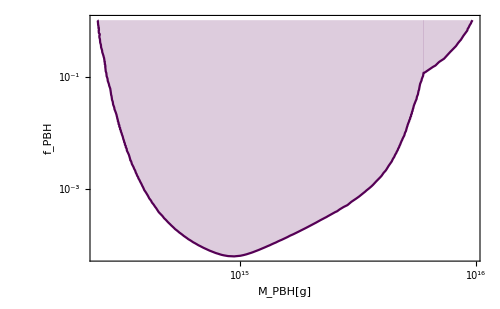

```mathematica
p9=Show[ListPlot[Table[{astarsuperk1[[i,1]],astarsuperk1[[i,2]]},{i,50,Length[astarsuperk1]}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top],
ListPlot[Table[{astarkamland1[[i,1]],astarkamland1[[i,2]]},{i,1,Length[astarkamland1]-131}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top]]
```

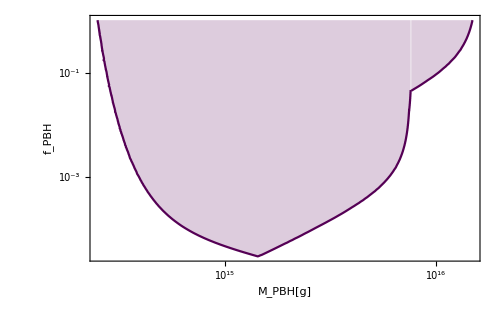

```mathematica
p9999=Show[ListPlot[Table[{astarsuperk2[[i,1]],astarsuperk2[[i,2]]},{i,90,Length[astarsuperk2]}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top],
ListPlot[Table[{astarkamland2[[i,1]],astarkamland2[[i,2]]},{i,238,Length[astarkamland2]}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top]]
```

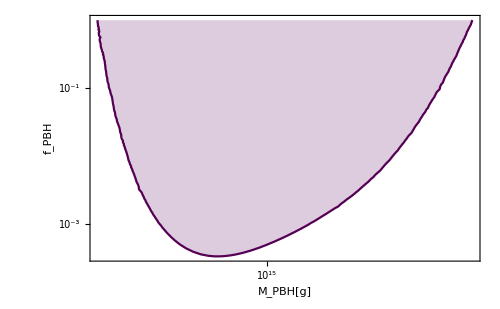

```mathematica
p5=Show[ListPlot[Table[{astarsuperk3[[i,1]],astarsuperk3[[i,2]]},{i,1,Length[astarsuperk3]}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top],
ListPlot[Table[{astarkamland3[[i,1]],astarkamland3[[i,2]]},{i,Length[astarkamland3],Length[astarkamland3]}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top]]
```

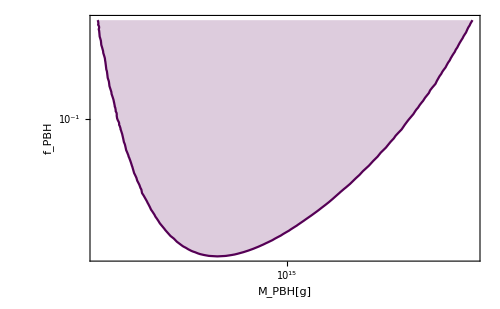

```mathematica
p0=Show[ListPlot[Table[{astarsuperk4[[i,1]],astarsuperk4[[i,2]]},{i,1,Length[astarsuperk4]}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top],
ListPlot[Table[{astarkamland4[[i,1]],astarkamland4[[i,2]]},{i,Length[astarkamland4],Length[astarkamland4]}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top]]
```

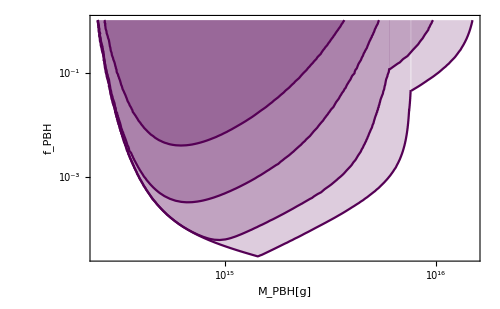

```mathematica
Show[p0,p5,p9,p9999]
```

```mathematica
(*COMBINING KAMLAND AND SUPER-K *)(*WITH EXTRAGALACTIC*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
astarkamland1=Import["kamland_astar_0.9_eg.dat","Table"];
```

```mathematica
astarkamland2=Import["kamland_astar_0.9999_eg.dat","Table"];
astarkamland3=Import["kamland_astar_0.5_eg.dat","Table"];
astarkamland4=Import["kamland_astar_0_eg.dat","Table"];
```

```mathematica
astarsuperk1=Import["superk_astar_0.9_eg.dat","Table"];
```

```mathematica
astarsuperk2=Import["superk_astar_0.9999_eg.dat","Table"];
astarsuperk3=Import["superk_astar_0.5_eg.dat","Table"];
astarsuperk4=Import["superk_astar_0_eg.dat","Table"];
```

```mathematica
myticks={{{{-9,"10^-9",{0.020,0}},{Log10[2*10^-9],"",{0.010,0}},{Log10[4*10^-9],"",{0.010,0}},{Log10[6*10^-9],"",{0.010,0}},{Log10[8*10^-9],"",{0.010,0}},{-8,"10^-8",{0.020,0}},{Log10[2*10^-8],"",{0.010,0}},{Log10[4*10^-8],"",{0.010,0}},{Log10[6*10^-8],"",{0.010,0}},{Log10[8*10^-8],"",{0.010,0}},{-7,"10^-7",{0.020,0}},{Log10[2*10^-7],"",{0.010,0}},{Log10[4*10^-7],"",{0.010,0}},{Log10[6*10^-7],"",{0.010,0}},{Log10[8*10^-7],"",{0.010,0}},{-6,"10^-6",{0.020,0}},{Log10[2*10^-6],"",{0.010,0}},{Log10[4*10^-6],"",{0.010,0}},{Log10[6*10^-6],"",{0.010,0}},{Log10[8*10^-6],"",{0.010,0}},{-5,"10^-5",{0.020,0}},{Log10[2*10^-5],"",{0.010,0}},{Log10[4*10^-5],"",{0.010,0}},{Log10[6*10^-5],"",{0.010,0}},{Log10[8*10^-5],"",{0.010,0}},{-4,"10^-4",{0.020,0}},{Log10[2*10^-4],"",{0.010,0}},{Log10[4*10^-4],"",{0.010,0}},{Log10[6*10^-4],"",{0.010,0}},{Log10[8*10^-4],"",{0.010,0}},{-3,"10^-3",{0.020,0}},{Log10[2*10^-3],"",{0.010,0}},{Log10[4*10^-3],"",{0.010,0}},{Log10[6*10^-3],"",{0.010,0}},{Log10[8*10^-3],"",{0.010,0}},{-2,"10^-2",{0.020,0}},{Log10[2*10^-2],"",{0.010,0}},{Log10[4*10^-2],"",{0.010,0}},{Log10[6*10^-2],"",{0.010,0}},{Log10[8*10^-2],"",{0.010,0}},{-1,"10^-1",{0.020,0}},{Log10[2*10^-1],"",{0.010,0}},{Log10[4*10^-1],"",{0.010,0}},{Log10[6*10^-1],"",{0.010,0}},{Log10[8*10^-1],"",{0.010,0}}{0,"10^0",{0.020,0}}},None},

{{{14,"10^14",{0.020,0}},{Log10[2*10^14],"",{0.010,0}},{Log10[4*10^14],"",{0.010,0}},{Log10[6*10^14],"",{0.010,0}},{Log10[8*10^14],"",{0.010,0}},{15,"10^15",{0.020,0}},{Log10[2*10^15],"",{0.010,0}},{Log10[4*10^15],"",{0.010,0}},{Log10[6*10^15],"",{0.010,0}},{Log10[8*10^15],"",{0.010,0}},{16,"10^16",{0.020,0}},{Log10[2*10^16],"",{0.010,0}},{Log10[4*10^16],"",{0.010,0}},{Log10[6*10^16],"",{0.010,0}},{Log10[8*10^16],"",{0.010,0}},{17,"10^17",{0.020,0}},{Log10[2*10^17],"",{0.010,0}},{Log10[4*10^17],"",{0.010,0}},{Log10[6*10^17],"",{0.010,0}},{Log10[8*10^17],"",{0.010,0}},{18,"10^18",{0.020,0}},{Log10[2*10^18],"",{0.010,0}},{Log10[4*10^18],"",{0.010,0}},{Log10[6*10^18],"",{0.010,0}},{Log10[8*10^18],"",{0.010,0}},{19,"10^19",{0.020,0}},{Log10[2*10^19],"",{0.010,0}},{Log10[4*10^19],"",{0.010,0}},{Log10[6*10^19],"",{0.010,0}},{Log10[8*10^19],"",{0.010,0}},{20,"10^20",{0.020,0}},{Log10[2*10^20],"",{0.010,0}},{Log10[4*10^20],"",{0.010,0}},{Log10[6*10^20],"",{0.010,0}},{Log10[8*10^20],"",{0.010,0}},{21,"10^21",{0.020,0}},{Log10[2*10^21],"",{0.010,0}},{Log10[4*10^21],"",{0.010,0}},{Log10[6*10^21],"",{0.010,0}},{Log10[8*10^21],"",{0.010,0}},{22,"10^22",{0.020,0}},{Log10[2*10^22],"",{0.010,0}},{Log10[4*10^22],"",{0.010,0}},{Log10[6*10^22],"",{0.010,0}},{Log10[8*10^22],"",{0.010,0}},{23,"10^23",{0.020,0}},{Log10[2*10^23],"",{0.010,0}},{Log10[4*10^23],"",{0.010,0}},{Log10[6*10^23],"",{0.010,0}},{Log10[8*10^23],"",{0.010,0}},{24,"10^24",{0.020,0}}},None}};
```

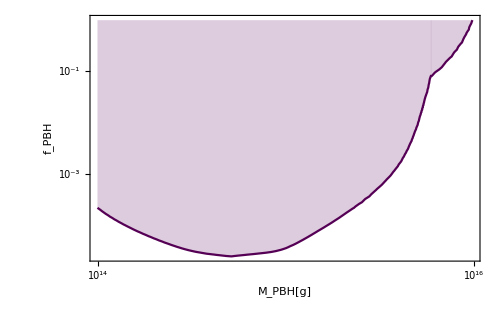

```mathematica
p9=Show[ListPlot[Table[{astarsuperk1[[i,1]],astarsuperk1[[i,2]]},{i,58,Length[astarsuperk1]}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top],
ListPlot[Table[{astarkamland1[[i,1]],astarkamland1[[i,2]]},{i,Length[astarkamland1]-137}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top]]
```

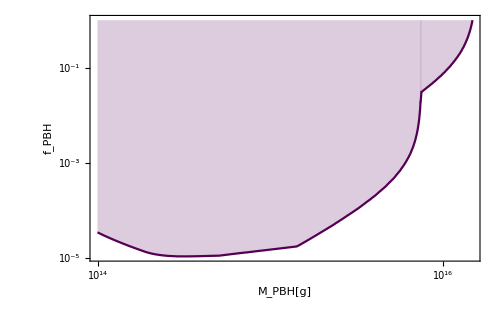

```mathematica
p9999=Show[ListPlot[Table[{astarsuperk2[[i,1]],astarsuperk2[[i,2]]},{i,102,Length[astarsuperk2]}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top],
ListPlot[Table[{astarkamland2[[i,1]],astarkamland2[[i,2]]},{i,1,Length[astarkamland2]-154}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top]]
```

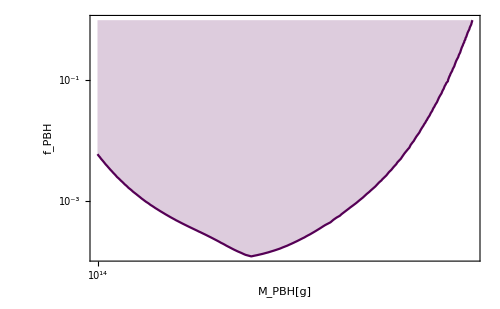

```mathematica
p5=Show[ListPlot[Table[{astarsuperk3[[i,1]],astarsuperk3[[i,2]]},{i,1,Length[astarsuperk3]}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top],
ListPlot[Table[{astarkamland3[[i,1]],astarkamland3[[i,2]]},{i,Length[astarkamland3],Length[astarkamland3]}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top]]
```

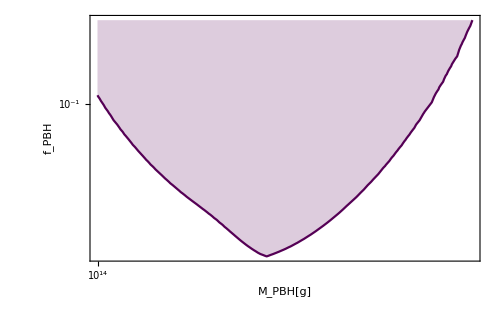

```mathematica
p0=Show[ListPlot[Table[{astarsuperk4[[i,1]],astarsuperk4[[i,2]]},{i,1,Length[astarsuperk4]}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top],
ListPlot[Table[{astarkamland4[[i,1]],astarkamland4[[i,2]]},{i,Length[astarkamland4],Length[astarkamland4]}],PlotStyle->Darker[Purple],Frame->True,FrameStyle->Directive[14, "Times",Black],Joined->True,FrameTicks->myticks,PlotRange->{{14,18},{0,-9}},ImageSize->500,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,Filling->Top]]
```

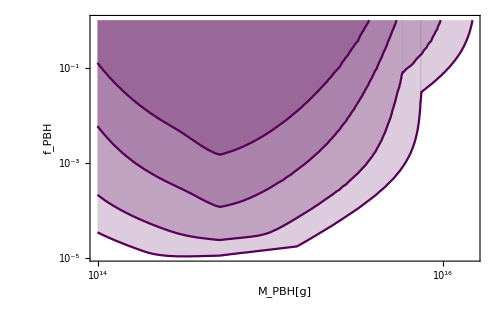

```mathematica
Show[p0,p5,p9,p9999]
```

```mathematica
(*CHECK*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ρ0=0.4;(*in Gev/cm^3*)
r0=8.5*10^3*3.086*10^18;(*in cm*)
rs=20*10^3*3.086*10^18;(*in cm*)
rmax=3*10^3*3.086*10^18;(*in cm*)
G=6.707*10^-39;(*In GeV^-2*)
ρ[r_]:=ρ0*(r/r0)^-1*((1+(r0/rs))/(1+(r/rs)))^2;
emax=3*10^-3;(*in GeV*)
emin=0.5*10^-3;(*in GeV*)

tage=4.32*10^17;
τ[mpbh_?NumericQ]:=3.28*10^-27*mpbh^3;
p[mpbh_?NumericQ]:=Exp[-tage/τ[mpbh]];
```

```mathematica
data1=Import["webber_interpol.dat","Table"];
data2=Import["interpolation.dat","Table"];
```

```mathematica
func=Interpolation[data1,InterpolationOrder->2];
func2=Interpolation[data2,InterpolationOrder->2];
```

```mathematica
ϕ[mpbh_?NumericQ,fpbh_?NumericQ]:=1/(2*π)*NIntegrate[(27*x^2*func[x])/(Exp[8*π*x]+1)*1/(G*mpbh*5.62*10^23),{x,G*mpbh*5.62*10^23*emin,G*mpbh*5.62*10^23*emax}]*NIntegrate[4*π*r^2*ρ[r],{r,0,rmax}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24;
ϕ2[mpbh_?NumericQ,fpbh_?NumericQ]:=1/(2*π)*NIntegrate[(27*x^2*func2[x])/(Exp[8*π*x]+1)*1/(G*mpbh*5.62*10^23),{x,G*mpbh*5.62*10^23*emin,G*mpbh*5.62*10^23*emax}]*NIntegrate[4*π*r^2*ρ[r],{r,0,rmax}]/(mpbh*5.62*10^23)*fpbh*1.52*10^24;
```

```mathematica
myticks={{{{-9,"10^-9",{0.020,0}},{Log10[2*10^-9],"",{0.010,0}},{Log10[4*10^-9],"",{0.010,0}},{Log10[6*10^-9],"",{0.010,0}},{Log10[8*10^-9],"",{0.010,0}},{-8,"10^-8",{0.020,0}},{Log10[2*10^-8],"",{0.010,0}},{Log10[4*10^-8],"",{0.010,0}},{Log10[6*10^-8],"",{0.010,0}},{Log10[8*10^-8],"",{0.010,0}},{-7,"10^-7",{0.020,0}},{Log10[2*10^-7],"",{0.010,0}},{Log10[4*10^-7],"",{0.010,0}},{Log10[6*10^-7],"",{0.010,0}},{Log10[8*10^-7],"",{0.010,0}},{-6,"10^-6",{0.020,0}},{Log10[2*10^-6],"",{0.010,0}},{Log10[4*10^-6],"",{0.010,0}},{Log10[6*10^-6],"",{0.010,0}},{Log10[8*10^-6],"",{0.010,0}},{-5,"10^-5",{0.020,0}},{Log10[2*10^-5],"",{0.010,0}},{Log10[4*10^-5],"",{0.010,0}},{Log10[6*10^-5],"",{0.010,0}},{Log10[8*10^-5],"",{0.010,0}},{-4,"10^-4",{0.020,0}},{Log10[2*10^-4],"",{0.010,0}},{Log10[4*10^-4],"",{0.010,0}},{Log10[6*10^-4],"",{0.010,0}},{Log10[8*10^-4],"",{0.010,0}},{-3,"10^-3",{0.020,0}},{Log10[2*10^-3],"",{0.010,0}},{Log10[4*10^-3],"",{0.010,0}},{Log10[6*10^-3],"",{0.010,0}},{Log10[8*10^-3],"",{0.010,0}},{-2,"10^-2",{0.020,0}},{Log10[2*10^-2],"",{0.010,0}},{Log10[4*10^-2],"",{0.010,0}},{Log10[6*10^-2],"",{0.010,0}},{Log10[8*10^-2],"",{0.010,0}},{-1,"10^-1",{0.020,0}},{Log10[2*10^-1],"",{0.010,0}},{Log10[4*10^-1],"",{0.010,0}},{Log10[6*10^-1],"",{0.010,0}},{Log10[8*10^-1],"",{0.010,0}}{0,"10^0",{0.020,0}}},None},

{{{14,"10^14",{0.020,0}},{Log10[2*10^14],"",{0.010,0}},{Log10[3*10^14],"",{0.010,0}},{Log10[4*10^14],"",{0.010,0}},{Log10[5*10^14],"",{0.010,0}},{Log10[6*10^14],"",{0.010,0}},{Log10[7*10^14],"",{0.010,0}},{Log10[8*10^14],"",{0.010,0}},{Log10[9*10^14],"",{0.010,0}},{15,"10^15",{0.020,0}},{Log10[2*10^15],"",{0.010,0}},{Log10[3*10^15],"",{0.010,0}},{Log10[4*10^15],"",{0.010,0}},{Log10[5*10^15],"",{0.010,0}},{Log10[6*10^15],"",{0.010,0}},{Log10[7*10^15],"",{0.010,0}},{Log10[8*10^15],"",{0.010,0}},{Log10[9*10^15],"",{0.010,0}},{16,"10^16",{0.020,0}},{Log10[2*10^16],"",{0.010,0}},{Log10[3*10^16],"",{0.010,0}},{Log10[4*10^16],"",{0.010,0}},{Log10[5*10^16],"",{0.010,0}},{Log10[6*10^16],"",{0.010,0}},{Log10[7*10^16],"",{0.010,0}},{Log10[8*10^16],"",{0.010,0}},{Log10[9*10^16],"",{0.010,0}},{17,"10^17",{0.020,0}},{Log10[2*10^17],"",{0.010,0}},{Log10[3*10^17],"",{0.010,0}},{Log10[4*10^17],"",{0.010,0}},{Log10[5*10^17],"",{0.010,0}},{Log10[6*10^17],"",{0.010,0}},{Log10[7*10^17],"",{0.010,0}},{Log10[8*10^17],"",{0.010,0}},{Log10[9*10^17],"",{0.010,0}},{18,"10^18",{0.020,0}}},None}};
```

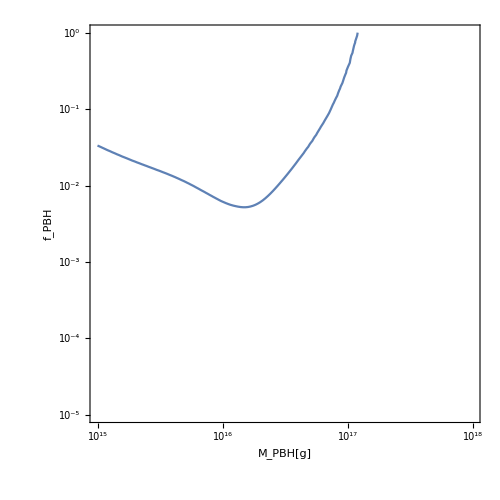

```mathematica
ContourPlot[{ϕ[10^x,10^y]==2*10^43},{x,15,18},{y,0,-5},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,GridLines->None,ImageSize->500,PlotPoints->20]
```

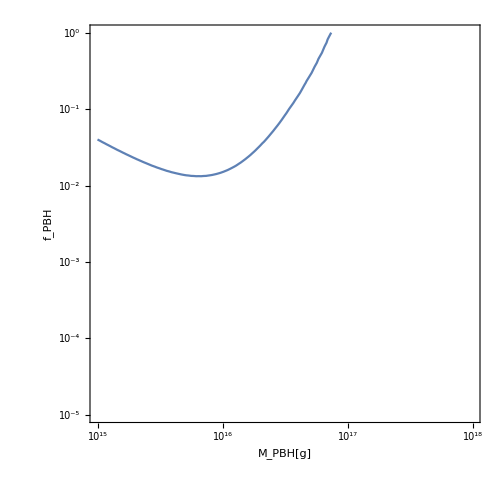

```mathematica
ContourPlot[{ϕ2[10^x,10^y]==2*10^43},{x,15,18},{y,0,-5},Frame->True,FrameStyle->Directive[14, "Times",Black],FrameTicks->myticks,FrameLabel->{Style["M_PBH[g]",FontSize->20,Bold],Style["f_PBH",FontSize->20,Bold]},PlotRangePadding->None,GridLines->None,ImageSize->500,PlotPoints->20]
```

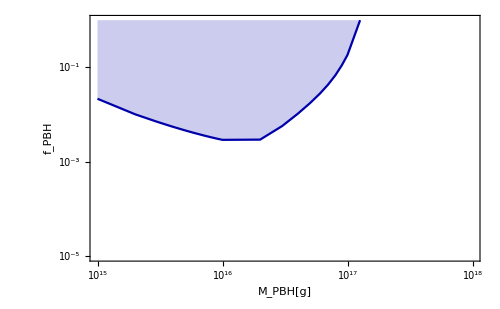
```mathematica
p=-Graphics-;
```

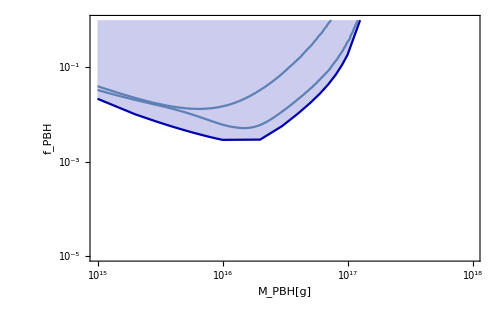

```mathematica
Show[-Graphics-,-Graphics-,-Graphics-]
```

```mathematica
myticks={{{{0.005,"0.005",{0.020,0}},{0.006,"",{0.010,0}},{0.007,"",{0.010,0}},{0.008,"",{0.010,0}},{0.009,"",{0.010,0}},{0.01,"",{0.010,0}},{0.02,"",{0.010,0}},{0.03,"",{0.010,0}},{0.04,"",{0.010,0}},{0.05,"0.05",{0.020,0}},{0.06,"",{0.010,0}},{0.07,"",{0.010,0}},{0.08,"",{0.010,0}},{0.09,"",{0.010,0}},{0.1,"",{0.010,0}},{0.2,"",{0.010,0}},{0.3,"",{0.010,0}},{0.4,"",{0.010,0}},{0.5,"0.5",{0.020,0}}},None},

{{{0.2,"0.2",{0.010,0}},{0.3,"",{0.010,0}},{0.4,"0.4",{0.010,0}},{0.5,"",{0.010,0}},{0.6,"0.6",{0.010,0}},{0.7,"",{0.010,0}},{0.8,"0.8",{0.010,0}},{0.9,"",{0.010,0}},{1.0,"1.0",{0.010,0}}},None}};
```

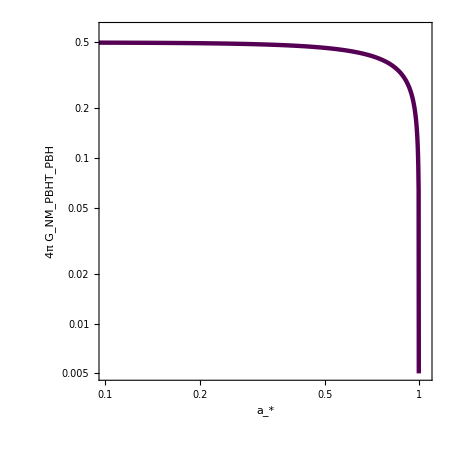

```mathematica
LogLogPlot[((1-astar^2)^0.5)/(1+(1-astar^2)^0.5),{astar,0,1},PlotStyle->Directive[Darker[Purple],Thickness[0.007]],PlotRange->{{10^-1,1.05},{0.005,0.6}},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.004]],ImageSize->450,AspectRatio->1,FrameLabel->{Style["a_*",FontSize->20],Style["4π G_NM_PBHT_PBH",FontSize->20]},FrameTicks->myticks]
```

```mathematica
f[astar_]:=((1-astar^2)^0.5)/(1+(1-astar^2)^0.5);
```

```mathematica
f[0]/f[0.9999]
```

f[0]/f[0.9999]

```mathematica
G=6.707*10^-39;(*In GeV^-2*)
```

```mathematica
T[mpbh_?NumericQ,astar_?NumericQ]:=1/(4*π*G*mpbh*5.62*10^23)*((1-astar^2)^0.5)/(1+(1-astar^2)^0.5); (*mpbh in g*)
```

```mathematica
myticks={{{{0.001,"0.001",{0.020,0}},{0.002,"",{0.010,0}},{0.003,"",{0.010,0}},{0.004,"",{0.010,0}},{0.005,"",{0.010,0}},{0.006,"",{0.010,0}},{0.007,"",{0.010,0}},{0.008,"",{0.010,0}},{0.009,"",{0.010,0}},{0.01,"0.01",{0.020,0}},{0.02,"",{0.010,0}},{0.03,"",{0.010,0}},{0.04,"",{0.010,0}},{0.05,"",{0.010,0}},{0.06,"",{0.010,0}},{0.07,"",{0.010,0}},{0.08,"",{0.010,0}},{0.09,"",{0.010,0}},{0.1,"0.1",{0.020,0}},{0.2,"",{0.010,0}},{0.3,"",{0.010,0}},{0.4,"",{0.010,0}},{0.5,"",{0.010,0}},{0.6,"",{0.010,0}},{0.7,"",{0.010,0}},{0.8,"",{0.010,0}},{0.9,"",{0.010,0}},{1,"1",{0.020,0}},{2,"",{0.010,0}},{3,"",{0.010,0}},{4,"",{0.010,0}},{5,"",{0.010,0}},{6,"",{0.010,0}},{7,"",{0.010,0}},{8,"",{0.010,0}},{9,"",{0.010,0}},{10,"10",{0.020,0}},{20,"",{0.010,0}},{30,"",{0.010,0}},{40,"",{0.010,0}},{50,"",{0.010,0}},{60,"",{0.010,0}},{70,"",{0.010,0}},{80,"",{0.010,0}},{90,"",{0.010,0}},{100,"100",{0.020,0}}},None},

{{{0.2,"0.2",{0.010,0}},{0.3,"",{0.010,0}},{0.4,"0.4",{0.010,0}},{0.5,"",{0.010,0}},{0.6,"0.6",{0.010,0}},{0.7,"",{0.010,0}},{0.8,"0.8",{0.010,0}},{0.9,"",{0.010,0}},{1.0,"1.0",{0.010,0}}},None}};
```

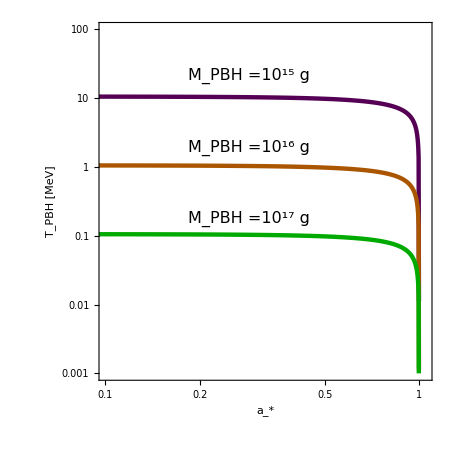

```mathematica
p1=LogLogPlot[{1000*T[10^15,astar],1000*T[10^16,astar],1000*T[10^17,astar]},{astar,0,1},PlotStyle->{Directive[Darker[Purple],Thickness[0.007]],Directive[Darker[Orange],Thickness[0.007]],Directive[Darker[Green],Thickness[0.007]]},PlotRange->{{10^-1,1.05},{0.001,100}},Frame->True,FrameStyle->Directive[14, "Times",Black,Thickness[0.004]],ImageSize->450,AspectRatio->1,FrameLabel->{Style["a_*",FontSize->20],Style["T_PBH [MeV]",FontSize->20]},FrameTicks->myticks,Epilog->{Text[Style["M_PBH =10^15 g",Black,16],Scaled[{.45,.85}]],Text[Style["M_PBH =10^16 g",Black,16],Scaled[{.45,.65}]],Text[Style["M_PBH =10^17 g",Black,16],Scaled[{.45,.45}]]}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["astar_variation.pdf",p1];
```

```mathematica
NSolve[4.02*T[mpbh,0]*1000==1,mpbh]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{mpbh→4.24347×10^16}}

```mathematica
T[4.24*10^16,0.9999]*1000
```

0.00694329

```mathematica
T[4.24*10^16,0]*1000
```

0.24896

```mathematica
(*1106.0011*)
```

```mathematica
Integrate[Integrate[(2 ρDM L)/(mBH vSolar σ) Sqrt[π/En] Exp[-(2 En+vSolar^2)/(2 σ^2)] Sinh[(vSolar Sqrt[2 En])/σ^2],{L,0,Sqrt[2 RSolar (GN M+En RSolar)]}],{En,0,∞}]//FullSimplify
```

ConditionalExpression[(RSolar ρDM (ⅇ^(-vSolar^2/(2 σ^2)) √(2 π) RSolar σ+(π (2 GN M+RSolar (vSolar^2+σ^2)) Erf[vSolar/(√2 σ)])/vSolar))/mBH,Re[σ^2]≥0]

```mathematica
(*Sun*)
ρ=0.3*1.78*10^-21;(*in kg/m^3*)
R=6.95*10^8;(*in m*)
vsolar=220*10^3;(*in m/sec*)
M=2*10^30;(*in kg*)
G=6.674*10^-11;(*in SI*)
num[mpbh_]:=(π*R^2*ρ*vsolar)/(mpbh*10^-3)*(1/(E*π^0.5)+Erf[1]*(1.5+(2*G*M)/(R*vsolar^2)))*3.15*10^7;(*in yr^-1*)
num[10^21]
```

4.58203×10^-8

```mathematica
(*Nearest Red Giant GACRUX*)
ρ=0.4*1.78*10^-21;(*in kg/m^3*)
R=84*6.95*10^8;(*in m*)
vsolar=220*10^3;(*in m/sec*)
M=1.5*2*10^30;(*in kg*)
G=6.674*10^-11;(*in SI*)
num[mpbh_]:=(π*R^2*ρ*vsolar)/(mpbh*10^-3)*(1/(E*π^0.5)+Erf[1]*(1.5+(2*G*M)/(R*vsolar^2)))*3.15*10^7;(*in yr^-1*)
num[10^20]
```

0.000840563

```mathematica
regrb=(4*6.707*10^-39*10^-15*2*10^33*5.62*10^23*3*10^27*10^14/1.98)^0.5*1.98*10^-14(*in cm*)
```

1.33835×10^9

```mathematica
refrb=(4*6.707*10^-39*10^-4*2*10^33*5.62*10^23*3*10^27*10^14/1.98)^0.5*1.98*10^-14(*in cm*)
```

4.23224×10^14